# ปัญหาเข็มของบึฟฟอง (Buffon' s Needle)

## ไปอ่านเอาเองได้ที่ https://en.wikipedia.org/wiki/Buffon%27s_needle

```mathematica
genNeedle[{x_,y_},θ_,len_]:=Line[{{(x+0.5len Cos[θ]),(y+0.5Sin[θ])},{(x-0.5len Cos[θ]),(y-0.5 len Sin[θ])}}]
```

```mathematica
horizontalLine[diff_,len_,{x0_,y0_},n_]:=Table[Line[{{x0,y0+(i diff)},{len,y0+(i diff)}}],{i,n}]
```

```mathematica
estimatedPi[needlelength_,nneedles_,linespace_,ncross_]:=2.*needlelength*nneedles /(linespace*ncross)
```

```mathematica
run[nl_,nfl_,ll_,diff_]:=Module[{fls,ls,outls,pnts,ncross},fls=horizontalLine[diff,10,{0,0},nfl];
ls=Table[genNeedle[{RandomReal[{0,10}],RandomReal[{0,nfl*diff}]},RandomReal[π],ll],{nl}];
outls=Table[Solve[{x,y}∈RegionIntersection[fls[[i]],#],{x,y}]&/@ls,{i,Length@fls}];
pnts=Point[{x,y}]/.Flatten[outls,2];
ncross=Length@Flatten[outls,2];
Graphics[{fls,ls,Red,PointSize[Medium],If[Length@Flatten[outls,2]>0,pnts]},PlotLabel->Style["จำนวนเข็มที่ทับเส้น:"<>ToString@ncross<>" π≈"<>ToString@estimatedPi[ll,nl,diff,ncross],FontSize->20,Bold]]];
```

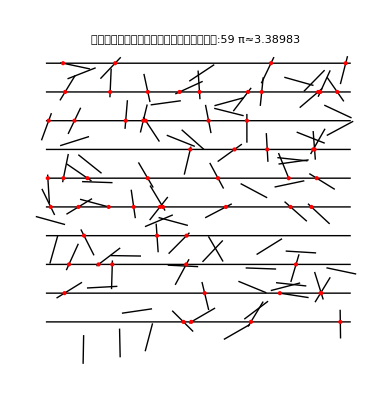

```mathematica
nlines = 10;
nneedles=100;
linelength=1;
linespace=1;
run[nneedles,nlines,linelength, linespace]
```